0 | {0,0,0,0} | {{0→0,True}}
1 | {0,0,0,1} | {{1→0,d+r<1+d p},{1→1,d+r>1+d p}}
2 | {0,0,1,0} | {{2→0,True}}
3 | {0,0,1,1} | {{3→0,True}}
4 | {0,1,0,0} | {{4→0,d<p+d p},{4→13,d>p+d p}}
5 | {0,1,0,1} | {{5→0,(p+r<1&&d<p+d p)||(p+r≥1&&d+r<1+d p)},{5→3,2 r>1&&p+r>1&&(-1+r)/(-1+p)<d<p/r},{5→12,p+r<1&&d>p+d p&&r+d r<1},{5→15,(p+r≤1&&r+d r>1)||(p+r>1&&d r>p)}}
6 | {0,1,1,0} | {{6→0,d<p},{6→9,d>p}}
7 | {0,1,1,1} | {{7→0,d<p},{7→8,d>p}}
8 | {1,0,0,0} | {{8→0,True}}
9 | {1,0,0,1} | {{9→0,(1+d) r<1+d p},{9→9,(1+d) r>1+d p}}
10 | {1,0,1,0} | {{10→0,True}}
11 | {1,0,1,1} | {{11→0,True}}
12 | {1,1,0,0} | {{12→0,True}}
13 | {1,1,0,1} | {{13→0,(1+d) r<1+d p},{13→11,(1+d) r>1+d p}}
14 | {1,1,1,0} | {{14→0,True}}
15 | {1,1,1,1} | {{15→0,True}}

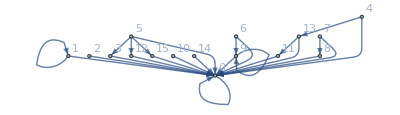

256

```mathematica
values = {t==1,s==0};
restrictions = {t>r>p>s,0<d<1};

outside = values[[All,1]];
inside = DeleteCases[restrictions[[1]] /.{Greater->List},Alternatives @@ outside];

changes = values/.{Equal->Rule};
restrictions= restrictions/.changes;
restrictions = Flatten[AppendTo[restrictions,values]];
result[i_, strats_]:=
Module[{input = i, str = strats},
output = {};
transpoints = {};
Do[{
strat = str[[j]];
assumptions = Flatten[{
               If[strat[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[strat[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[strat[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[strat[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111],
               restrictions}];

Assuming[assumptions,
{q1 = Simplify[Boole[Q2000>Q2001] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2000<Q2001] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q2=  Simplify[Boole[Q2000>Q2001] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2000<Q2001] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q3=  Simplify[Boole[Q2100>Q2101] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2100<Q2101] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q4=  Simplify[Boole[Q2100>Q2101] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2100<Q2101] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q5=  Simplify[Boole[Q2010>Q2011] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2010<Q2011] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q6=  Simplify[Boole[Q2010>Q2011] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2010<Q2011] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q7=  Simplify[Boole[Q2110>Q2111] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                         Boole[Q2110<Q2111] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q8=  Simplify[Boole[Q2110>Q2111] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                         Boole[Q2110<Q2111] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])]
}];
sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
formula1 = Simplify[Assuming[assumptions,
 Simplify[Reduce[
  If[strat[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[strat[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] && 
If[strat[[3]]==0,Simplify[sol1[[1]][[5]][[2]] > sol1[[1]][[6]][[2]]], Simplify[sol1[[1]][[5]][[2]] < sol1[[1]][[6]][[2]]]] && 
If[strat[[4]]==0,Simplify[sol1[[1]][[7]][[2]] > sol1[[1]][[8]][[2]]], Simplify[sol1[[1]][[7]][[2]] < sol1[[1]][[8]][[2]]]],d,Reals]]]];
If[(formula1 === False)==False , AppendTo[output,{FromDigits[i,2]->j-1,Simplify[formula1]}]];
},{j,1,16}];
output
];

strats = {};
Do[AppendTo[strats, Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,15}];


transitions = {};
Do[AppendTo[transitions,result[strats[[i]],strats]],{i,1,16}];
Amount = 1;
Do[Amount *= Length[transitions[[i]]],{i,1,16}];

grid = {};
Do[AppendTo[grid,{FromDigits[strats[[i]],2], strats[[i]],transitions[[i]]}],{i,1,16}]
Grid[grid,Frame->All]

edges = {};
Do[Do[AppendTo[edges, transitions[[i]][[j]][[1]]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}];

labels = {};
Do[Do[AppendTo[labels, transitions[[i]][[j]][[1]] -> transitions[[i]][[j]][[2]]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}];

GraphPlot[edges, VertexLabels->Automatic,  DirectedEdges->True, ImageSize->Full]
Amount
```

```mathematica
(*formulas = {};
edgelist = {};

formulas = Tuples[transitions][[All,All,2]];
edgelist = Tuples[transitions][[All,All,1]];

Graphs = {};
formulas = Table[FullSimplify[formulas[[i]] /. {List -> And}],{i,1,Length[formulas]}];
Graphs = Table[{edgelist[[i]],formulas[[i]]},{i,1,Length[formulas]}];
Graphs = DeleteCases[Graphs,x_ /; FindInstance[FullSimplify[Flatten[{x[[2]],restrictions}] /. {List -> And}],{d,t,r,p,s}] == {}];
Grid[Graphs, Frame->All]

*)
possible = {};
Do[
next = {};
Do[
If[possible == {},next=AppendTo[next,{transitions[[i]][[j]][[1]],transitions[[i]][[j]][[2]]}],
Do[
function = Assuming[restrictions,FullSimplify[And[possible[[k]][[2]],transitions[[i]][[j]][[2]]]]];
If[(function===False)==False,
next = AppendTo[next,{Flatten[{possible[[k]][[1]],transitions[[i]][[j]][[1]]}],Assuming[restrictions,FullSimplify[And[possible[[k]][[2]],function]]]}];
];
,{k,1,Length[possible]}];
];
,{j,1,Length[transitions[[i]]]}];
possible = next;
,{i,1,16}];        
Graphs = possible;
Length[Graphs]
Grid[Table[{i,Graphs[[i]][[2]]},{i,1,Length[Graphs]}], Frame->All]
(* Makes sure we have the right region*)
todraw = Table[FullSimplify[And[Graphs[[All,2]][[i]], And @@ restrictions[[;;-3]]]],{i,1,Length[Graphs[[All,2]]]}];
```

12

1 | d<p&&d+r<1+d p
2 | d<p&&1+d p<d+r&&(1+d) r<1+d p
3 | d<p+d p&&d+r<1+d p&&d>p
4 | 1+d p<d+r&&d r<p&&d>p&&1+d p>r+d r
5 | d+r<1+d p&&d>p+d p
6 | r+d r<1&&d+r>1+d p
7 | 1+d p>r+d r&&p+d p>d&&d r>p
8 | r+d r<1+d p&&d>p+d p&&d+r>1+d p&&(p+r>1||r+d r>1)
9 | d<p&&1+d p<r+d r
10 | 1+d p<r+d r&&d r<p&&d>p
11 | d<p+d p&&d r>p&&(1+d) r>1+d p
12 | 1+d p<r+d r&&p+d p<d

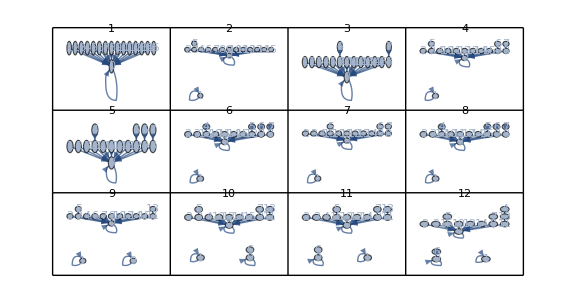

{d==p,d+r==1+d p,1+d p==d+r,(1+d) r==1+d p,d==p+d p,d r==p,1+d p==r+d r,r+d r==1,p+d p==d,r+d r==1+d p,p+r==1,r==s}

```mathematica
edgeslist = Graphs[[All,1]];

grid = ArrayReshape[Table[Graphics[GraphPlot[edgeslist[[i]], VertexLabels->Placed[Automatic,Center],VertexSize->.75,  DirectedEdges->True,PlotLabel->i,PlotStyle->Thick, GraphLayout->"LayeredDigraphEmbedding"]],{i,1,Length[edgeslist]}],{Ceiling[Sqrt[Length[Graphs]]],Ceiling[Sqrt[Length[Graphs]]]}];

Do[Do[If[grid[[i]][[j]]==0, grid[[i]][[j]] = Graphics[{}]],{j,1,Length[grid[[i]]]}],{i,1,Length[grid]}]
Do[If[grid[[i]] == ConstantArray[Graphics[{}],Length[grid[[i]]]],grid = grid[[1;;i-1]]; Break[]],{i,1,Length[grid]}]
GraphicsGrid[grid,Frame->All,ImageSize->Large]

(*
draw2[f_,l_]:=
Module[{formulas= f,legends=l},
 RegionPlot3D[{formulas[[1]],formulas[[2]],formulas[[3]],formulas[[4]],formulas[[5]],formulas[[6]],formulas[[7]],formulas[[8]],formulas[[9]],formulas[[10]],formulas[[11]],formulas[[12]]},{r,0,1},{p,0,1},{d,0,1},AxesLabel->Automatic, PlotStyle->Directive[Opacity[0.5]],Mesh->None,BoundaryStyle->Thick,PlotLegends->l,PerformanceGoal->"Quality"]
];

draw2[Graphs[[All,2]],Graphs[[All,2]]]*)


draw[f_,n_]:=
Module[{new = n,formulas= f},
formulas = ReplaceAll[formulas, {d->new,inside[[1]]->x,inside[[2]]->y}];
 RegionPlot[formulas,{x,0,1},{y,0,1},AxesLabel->Automatic, PlotStyle->{Pink,Red,Orange,Yellow,Green,Cyan,Blue,Magenta,Purple,Brown,Gray,Black},BoundaryStyle->Black,PlotLegends->Automatic,PerformanceGoal->"Quality",FrameLabel->{inside[[1]],inside[[2]]}]
];
(* Makes sure we have the right region*)
todraw = Table[FullSimplify[And[Graphs[[All,2]][[i]], And @@ restrictions[[;;-3]]]],{i,1,Length[Graphs[[All,2]]]}];
Manipulate[draw[todraw,d],{d,0,1}]

test = Graphs[[All,2]];
test = test /. {And -> List, Or->List,Less -> Equal, LessEqual->Equal,Greater->Equal,GreaterEqual->Equal };
test = AppendTo[test,r==s];
test = DeleteDuplicates[Flatten[test]]

drawLines[f_,n_]:=
Module[{new = n,formulas= f},
formulas = ReplaceAll[formulas, {d->new,inside[[1]]->x,inside[[2]]->y}];
 ContourPlot[Evaluate @(formulas),{x,0,1},{y,0,1},FrameLabel->{inside[[1]],inside[[2]]},BoundaryStyle->{Pink,Red,Orange,Yellow,Green,Cyan,Blue,Magenta,Purple,Brown,Gray,Black},PlotLegends->test]
];
Manipulate[drawLines[test,d],{d,0,1}]

(*
graphic = draw[todraw,1/2];
Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/d=0.5.png",graphic]
*)
```

```mathematica
postrans = DeleteDuplicates[Flatten[Graphs[[All,1]]]];
regions = {};
Do[AppendTo[regions,Position[Graphs,postrans[[i]]][[All,1]]],{i,1,Length[postrans]}];
regions = Table[todraw[[regions[[i]]]],{i,1,Length[regions]}];
regions = Table[regions[[i]] /. {List -> Or},{i,1,Length[regions]}];

drawtest[f_,n_,l_]:=
Module[{formulas = f, new = n,legend=l},
formulas = formulas /. {d->new,inside[[1]]->x,inside[[2]]->y};
If[formulas!={},
p1 = RegionPlot[formulas,{x,0,1},{y,0,1},FrameLabel->{inside[[1]],inside[[2]]},PerformanceGoal->"Quality",PlotLegends->legend,FrameTicksStyle->15,FrameStyle->15];
Show[p1]]
];

drawtest3D[f_]:=
Module[{formulas = f},
formulas = formulas /. {List->And,inside[[1]]->x,inside[[2]]->y};
RegionPlot3D[formulas,{x,0,1},{y,0,1},{d,0,1},PerformanceGoal->"Quality",PlotStyle->Directive[Specularity[White, 40],Orange],Mesh->None,AxesLabel->Automatic]
];

DynamicModule[{x={}},
{TogglerBar[Dynamic[x],
Table[{regions[[i]],postrans[[i]]} -> postrans[[i]],{i,1,Length[postrans]}],Appearance -> "Vertical" -> {Automatic,15}],
Manipulate[drawtest[x[[All,1]],d,x[[All,2]]],{d,0,1}],
Dynamic[drawtest3D[x[[All,1]]]]}
]
(*Total[Table[Area[ImplicitRegion[todraw[[i]] /.{d->1/2},{r,s}]],{i,1,Length[todraw]}]]*)
```

```mathematica
toBin[n_,l_]:= Join[ConstantArray[0,l-Length[IntegerDigits[n,2]]],IntegerDigits[n,2]]

grouping[g_]:=
Module[{gr = g},
group = GatherBy[gr,Last];
Do[
graphs = group[[i]][[1]][[3]];
condition = group[[i]][[1]][[2]];transitions =Table[group[[i]][[j]][[1]],{j,1,Length[group[[i]]]}];group[[i]]={transitions,condition,graphs},{i,1,Length[group]}];
group
]


trans = Table[{i-1->j-1 },{i,1,256},{j,1,256}];
transitions = ConstantArray[ConstantArray[{},256],256];
Do[Do[
from = {FromDigits[toBin[trans[[i,j,1,1]],8][[1;;4]],2],FromDigits[toBin[trans[[i,j,1,1]],8][[5;;8]],2]};
to= {FromDigits[toBin[trans[[i,j,1,2]],8][[5;;8]],2],FromDigits[toBin[trans[[i,j,1,2]],8][[1;;4]],2]};
regions = Intersection[Position[Graphs,from[[1]]->to[[1]]][[All,1]],Position[Graphs,from[[2]]->to[[2]]][[All,1]]];
conditions =  Table[todraw[[regions[[i]]]],{i,1,Length[regions]}];
AppendTo[transitions[[i]][[j]],{i-1->j-1,conditions,regions}],
{j,1,256}];
transitions[[i]]=DeleteCases[transitions[[i]],{{_Integer->_Integer,{},{}}}],
  {i,1,256}]

transitions = Flatten[transitions,2];

Do[transitions[[i]][[2]] = FullSimplify[Or @@ transitions[[i]][[2]]],{i,1,Length[transitions]}]
transitions = DeleteCases[transitions,{_Integer->_Integer,False,_}];

symmetric = Cases[transitions,HoldPattern[{a_->a_,_,_}]];

transitions=grouping[transitions];
(*legend2 = Table["[" <> ToString[transitions[[All,1,1]][[i]]] <> "]",{i, Length[transitions[[All,1,1,1]]]}];
DynamicModule[{x={}},
{TogglerBar[Dynamic[x],
Table[{transitions[[i]][[2]],legend2[[i]]} -> transitions[[i]][[1]],{i,1,Length[transitions]}],Appearance -> "Vertical" -> {Automatic,1}],
Manipulate[drawtest[x[[All,1]],d,x[[All,2]]],{d,0,1}]}
]*)

symmetric = grouping[symmetric];

legend = Table["[" <> ToString[symmetric[[All,1,1,1]][[i]]] <> "]",{i, Length[symmetric[[All,1,1,1]]]}];
DynamicModule[{x={}},
{TogglerBar[Dynamic[x],
Table[{symmetric[[i]][[2]],legend[[i]]} -> symmetric[[i]][[1]],{i,1,Length[symmetric]}],Appearance -> "Vertical" -> {Automatic,4}],
Manipulate[drawtest[x[[All,1]],d,x[[All,2]]],{d,0,1}]
}
]

(*RegionPlot[{0.3<(p)/(1-p),0.3<(1-t)/(t-p),0.3<p},{t,0,1},{p,0,1},PlotLegends->{(p-s)/(r-p),(r-t)/(t-p),(p-s)/(r-s)}]*)

(*symmetric[[3]][[2]]
Region[ImplicitRegion[symmetric[[3]][[2]],{d,t,p}]]
RegionPlot[Resolve[Exists[d,{d,t,p}∈ImplicitRegion[symmetric[[3]][[2]],{d,t,p}]]],{t,0,1},{p,0,1}]*)
```

```mathematica
statdistr[graph_] :=
Module[{g=graph},
distribution = ConstantArray[0,256];
Do[
pair = i-1;
path = {};
While[!MemberQ[path,pair],
     s1= FromDigits[toBin[pair,8][[1;;4]],2];
     s2 =FromDigits[toBin[pair,8][[5;;8]],2];
     t1 = g[[s2+1]][[2]];
     t2 = g[[s1+1]][[2]];
     path = AppendTo[path, pair];
     pair = FromDigits[Join[toBin[t1,4],toBin[t2,4]],2];
];
path = AppendTo[path, pair];
end = path[[Position[path,pair][[1]][[1]];;-2]];
Do[distribution[[end[[j]]+1]]+=(1/Length[end])/256,{j,1,Length[end]}]
,{i,1,256}];
distribution
] 

colpercent[index_,t_]:=
Module[{ind=index,type=t},
distr = statdistr[Graphs[[ind,1]]];
Sum[distr[[i]]*Boole[MemberQ[collist[[type]],i-1]],{i,1,256}]
]

percents = Table[Table[colpercent[j,i],{j,1,Length[Graphs[[All,1]]]}],{i,1,Length[collist]}]
```

{{0,0,0,0,0,0,0,0,3/256,1/32,1/32,1/32},{1,1,1,1,1,1,1,1,253/256,31/32,31/32,31/32}}

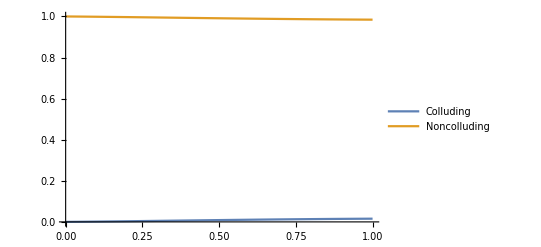

/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/Collusion Prisoner.png

```mathematica
colarea[delta_,type_]:=Sum[percents[[type]][[i]]*Area[ImplicitRegion[todraw[[i]]/.{d->delta,inside[[1]]->x,inside[[2]]->y},{x,y}]],{i,1,Length[todraw]}]
(*Plot[{colarea[x,1]*2,colarea[x,2]*2,colarea[x,3]*2},{x,0,1},PlotLegends->{"Colluding","Semicolluding","Noncolluding"}]*)
plot = Plot[{colarea[d,1]*2,colarea[d,2]*2},{d,0,1},PlotLegends->{"Colluding","Noncolluding"},PlotRange->{0,1}]
Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/Collusion Prisoner.png",plot]
```

```mathematica
weights = Import["/home/lars/Documents/Year 3/Bachelor project/Informatica/Python/network.csv"];
Do[weights[[i]]=Normalize[weights[[i]],Total],{i,1,16}];
weights= Flatten[weights];

edges = {};
Do[Do[AppendTo[edges,i->j],{j,1,16}],{i,1,16}]; 
Graph[edges,EdgeStyle->Thread[edges->Thread@{(Opacity[#]&/@weights),(Thickness[#/250]&/@weights)}],ImageSize->Full,VertexLabels->Automatic]
```

Import::nffil: File /home/lars/Documents/Year 3/Bachelor project/Informatica/Python/network.csv not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Set::partd: Part specification weights⟦i⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Set::partd: Part specification weights⟦i⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Set::partd: Part specification weights⟦i⟧ is longer than depth of object.

General::stop: Further output of Set::partd will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Thread::tdlen: Objects of unequal length in {1→1,1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,«246»}→{Opacity[$Failed],Thickness[($Failed)/250]} cannot be combined.

Graph[{1→1,1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,1→11,1→12,1→13,1→14,1→15,1→16,2→1,2→2,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,2→11,2→12,2→13,2→14,2→15,2→16,3→1,3→2,3→3,3→4,3→5,3→6,3→7,3→8,3→9,3→10,3→11,3→12,3→13,3→14,3→15,3→16,4→1,4→2,4→3,4→4,4→5,4→6,4→7,4→8,4→9,4→10,4→11,4→12,4→13,4→14,4→15,4→16,5→1,5→2,5→3,5→4,5→5,5→6,5→7,5→8,5→9,5→10,5→11,5→12,5→13,5→14,5→15,5→16,6→1,6→2,6→3,6→4,6→5,6→6,6→7,6→8,6→9,6→10,6→11,6→12,6→13,6→14,6→15,6→16,7→1,7→2,7→3,7→4,7→5,7→6,7→7,7→8,7→9,7→10,7→11,7→12,7→13,7→14,7→15,7→16,8→1,8→2,8→3,8→4,8→5,8→6,8→7,8→8,8→9,8→10,8→11,8→12,8→13,8→14,8→15,8→16,9→1,9→2,9→3,9→4,9→5,9→6,9→7,9→8,9→9,9→10,9→11,9→12,9→13,9→14,9→15,9→16,10→1,10→2,10→3,10→4,10→5,10→6,10→7,10→8,10→9,10→10,10→11,10→12,10→13,10→14,10→15,10→16,11→1,11→2,11→3,11→4,11→5,11→6,11→7,11→8,11→9,11→10,11→11,11→12,11→13,11→14,11→15,11→16,12→1,12→2,12→3,12→4,12→5,12→6,12→7,12→8,12→9,12→10,12→11,12→12,12→13,12→14,12→15,12→16,13→1,13→2,13→3,13→4,13→5,13→6,13→7,13→8,13→9,13→10,13→11,13→12,13→13,13→14,13→15,13→16,14→1,14→2,14→3,14→4,14→5,14→6,14→7,14→8,14→9,14→10,14→11,14→12,14→13,14→14,14→15,14→16,15→1,15→2,15→3,15→4,15→5,15→6,15→7,15→8,15→9,15→10,15→11,15→12,15→13,15→14,15→15,15→16,16→1,16→2,16→3,16→4,16→5,16→6,16→7,16→8,16→9,16→10,16→11,16→12,16→13,16→14,16→15,16→16},EdgeStyle→{1→1,1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,1→11,1→12,1→13,1→14,1→15,1→16,2→1,2→2,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,2→11,2→12,2→13,2→14,2→15,2→16,3→1,3→2,3→3,3→4,3→5,3→6,3→7,3→8,3→9,3→10,3→11,3→12,3→13,3→14,3→15,3→16,4→1,4→2,4→3,4→4,4→5,4→6,4→7,4→8,4→9,4→10,4→11,4→12,4→13,4→14,4→15,4→16,5→1,5→2,5→3,5→4,5→5,5→6,5→7,5→8,5→9,5→10,5→11,5→12,5→13,5→14,5→15,5→16,6→1,6→2,6→3,6→4,6→5,6→6,6→7,6→8,6→9,6→10,6→11,6→12,6→13,6→14,6→15,6→16,7→1,7→2,7→3,7→4,7→5,7→6,7→7,7→8,7→9,7→10,7→11,7→12,7→13,7→14,7→15,7→16,8→1,8→2,8→3,8→4,8→5,8→6,8→7,8→8,8→9,8→10,8→11,8→12,8→13,8→14,8→15,8→16,9→1,9→2,9→3,9→4,9→5,9→6,9→7,9→8,9→9,9→10,9→11,9→12,9→13,9→14,9→15,9→16,10→1,10→2,10→3,10→4,10→5,10→6,10→7,10→8,10→9,10→10,10→11,10→12,10→13,10→14,10→15,10→16,11→1,11→2,11→3,11→4,11→5,11→6,11→7,11→8,11→9,11→10,11→11,11→12,11→13,11→14,11→15,11→16,12→1,12→2,12→3,12→4,12→5,12→6,12→7,12→8,12→9,12→10,12→11,12→12,12→13,12→14,12→15,12→16,13→1,13→2,13→3,13→4,13→5,13→6,13→7,13→8,13→9,13→10,13→11,13→12,13→13,13→14,13→15,13→16,14→1,14→2,14→3,14→4,14→5,14→6,14→7,14→8,14→9,14→10,14→11,14→12,14→13,14→14,14→15,14→16,15→1,15→2,15→3,15→4,15→5,15→6,15→7,15→8,15→9,15→10,15→11,15→12,15→13,15→14,15→15,15→16,16→1,16→2,16→3,16→4,16→5,16→6,16→7,16→8,16→9,16→10,16→11,16→12,16→13,16→14,16→15,16→16}→{Opacity[$Failed],Thickness[($Failed)/250]},ImageSize→Full,VertexLabels→Automatic]

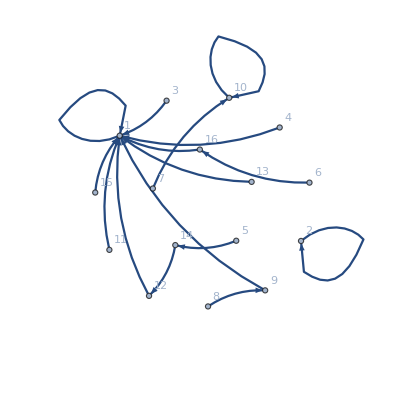

-Graphics-

```mathematica
inside
```

{r,p}